```mathematica
ClearAll["Global`*"];
(*Needs["PlotLegends`"]*)
μ=0.001; (*Viscocity of water [Pa*s] *)
ρ=998.2; (*Density of Water [kg/m^3]*)
g=9.81; (*[m/s^2]*)
hmax=0.165; (*Max fluid column height of 6.5 inches*)
d =1.19 *10^-3;(*Silastic Tubing inner diameter [m]*)
rs = d/2; (*Silastic Tubing inner Radius [m]*) 
A = π*(7.5*10^-3)^2; (*Area Cross-Section of a 10mL BD syringe [m^2]*)
L0=0.152; (*Tube length increment used. [m], 0152m=6"*)
Pmax6=1610; (*Hydrostatic Pressure from 6.5" tall reservoir [Pa]*)
Pmax14=3602; (*Hydrostatic Pressure from 14.5" tall reservoir [Pa]*)
P[h_]:=ρ*g*h;
RH[L_]:=(8*μ*L)/(π*rs^4) ;(*Hydraulic Resistance of Circular Silastic Channel*)
```

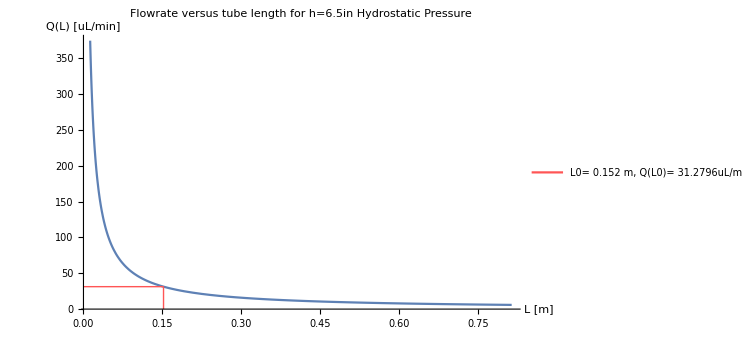

```mathematica
expr1=Pmax6/RH[L]*(60*10^6); (* For 2D Laminar Flow, ΔP=Q*R *)
expr2= Line[{{{L0,0},{L0,expr1/. L->L0}},{{0,expr1/. L->L0},{L0,expr1/. L->L0}}}];
(*For tubing lengths between 0.5in=0.0127m and 32in=0.813m*)
Plot[expr1,{L,0.0127,0.813},AxesLabel->{"L [m]","Q(L) [uL/min]"},PlotRange->All,PlotLabel->"Flowrate versus tube length for h=6.5in Hydrostatic Pressure",Epilog->{Lighter@Red, expr2},PlotLegends->{LineLegend[{Lighter@Red},{"L0= "<>TextString[L0]<>" m"<>",  Q(L0)= "<>TextString[Pmax6/RH[L0]*(60*10^6)]<>"uL/min"}]}]
```

```mathematica
(*For[i=1,i<=6,i++,Print["P=",Pmax6,"Pa, L ="<>TextString[i*L0]<>"m, Qmax =",Pmax6/RH[i*L0]*(60*10^6),"[uL/min]"]]
For[i=1,i<=6,i++,Print["P=",Pmax14,"Pa, L ="<>TextString[i*L0]<>"m, Qmax =",Pmax14/RH[i*L0]*(60*10^6),"[uL/min]"]]*)
```

```mathematica
(*Solve for max flowrate as a function of time Q(h(t))=A*dh/dt=(P(h))/R*)
hsol=DSolve[{-A*D[ht[t],t]==(P[ht[t]]/RH[L0]),ht[0]==hmax},ht[t],t];
h[t_] = FullSimplify[ht[t]/.hsol][[1]] ;
Qexprlist={};
Legendlist={};
Qexpr[t_,i_]:=P[h[t]]/RH[i*L0]*(60*10^6);
Do[AppendTo[Qexprlist,Qexpr[t,i]],{i,1,5}];
Do[AppendTo[Legendlist,"L="<>TextString[i*L0]<>"m"],{i,1,5}];
```

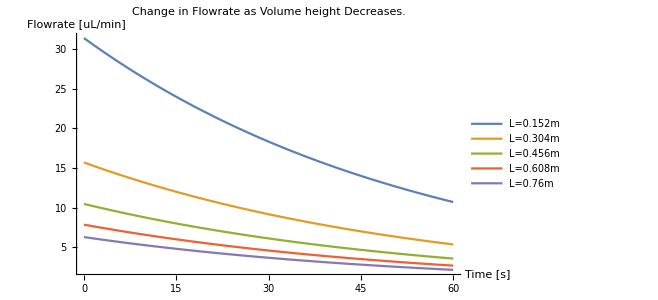

```mathematica
Plot [Qexprlist,{t,0,60},AxesLabel->{"Time [s]","Flowrate [uL/min]"},PlotRange->{0,All},PlotLabel->"Change in Flowrate as Volume height Decreases.",PlotLegends->Legendlist]
```